```mathematica
SetDirectory[NotebookDirectory[]];
```

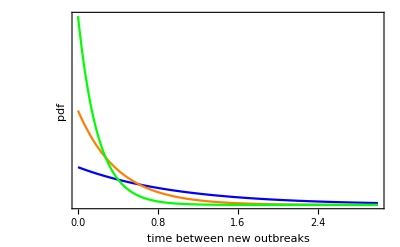

```mathematica
g1=Plot[{PDF[ExponentialDistribution[1],x],PDF[ExponentialDistribution[2.5],x],PDF[ExponentialDistribution[5],x]},{x,0,3},PlotRange->Full,Frame->{True,True,False,False},PlotStyle->{Blue,Orange,Green},FrameTicks->{True,False},FrameLabel->{"time between new outbreaks","pdf"},BaseStyle->Medium]
```

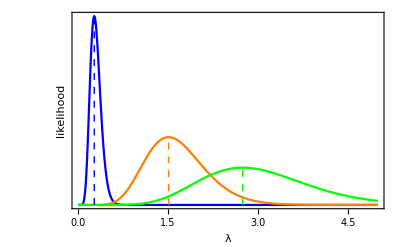

```mathematica
data1=RandomVariate[ExponentialDistribution[0.25],{10}];
data2=RandomVariate[ExponentialDistribution[1],{10}];
data3=RandomVariate[ExponentialDistribution[2],{10}];
int1 = NIntegrate[Likelihood[ExponentialDistribution[λ],data1],{λ,0,∞}];
int2 = NIntegrate[Likelihood[ExponentialDistribution[λ],data2],{λ,0,∞}];
int3 = NIntegrate[Likelihood[ExponentialDistribution[λ],data3],{λ,0,∞}];
g2=Plot[{Likelihood[ExponentialDistribution[λ],data1]/(2int1),Likelihood[ExponentialDistribution[λ],data2]/int2,Likelihood[ExponentialDistribution[λ],data3]/int3},{λ,0,5},PlotRange->Full,PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"λ","likelihood"},BaseStyle->Medium,Epilog->{{Dashed,Blue,Line[{{1/Mean@data1,0},{1/Mean@data1,Likelihood[ExponentialDistribution[1/Mean@data1],data1]/(2int1)}}]},{Dashed,Orange,Line[{{1/Mean@data2,0},{1/Mean@data2,Likelihood[ExponentialDistribution[1/Mean@data2],data2]/(int2)}}]},{Dashed,Green,Line[{{1/Mean@data3,0},{1/Mean@data3,Likelihood[ExponentialDistribution[1/Mean@data3],data3]/(int3)}}]}}]
```

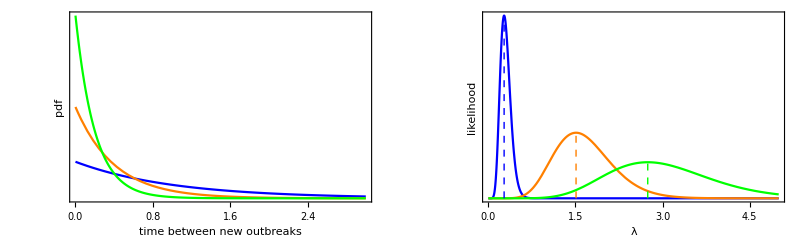

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_exponentialEbola.pdf",gFinal]
```

Distributions_exponentialEbola.pdf